# Sterile Neutrino (3 + 1)

## Survival Probability of Electron Neutrino

(0.824398 | 0.544564 | 0.154328 | 0.001
-0.518534 | 0.61732 | 0.59164 | 0.000999999
0.226916 | -0.567772 | 0.791292 | 0.000999999
-0.00053278 | -0.000594113 | -0.00153726 | 0.999999)

1-4 (0.+0.02325 Re[Sin[0.0030988 x]^2]+9.99999×10^-7 Re[Sin[1.27 x]^2])

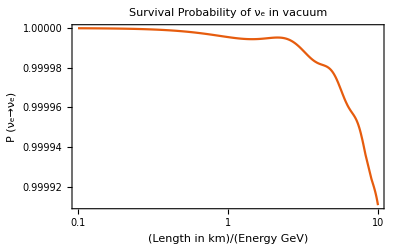

```mathematica
M11=M22=M33=M44=M12=M21=0;
M13=M23=M31=M32=24.4*10^-4;
M14=M24=M41=M42=1;
M34=M43=1;
M={{M11,M12,M13,M14},{M21,M22,M23,M24},{M31,M32,M33,M34},{M41,M42,M43, M44}};
MatrixForm[M];

theta12=0.5*ArcSin[Sqrt[0.846]];                                                
theta13=0.5*ArcSin[Sqrt[0.093]];    
theta23=0.5*ArcSin[Sqrt[0.92]];  
theta14=10^-3;                                                                                              
theta24=10^-3;                                                                                             
theta34=10^-3;                            

phase1=Exp[I*0];
phase2=Exp[I*0];
phase3=Exp[I*0];
Phase={{1,0,0,0},{0,phase1,0,0},{0,0,phase2,0},{0,0,0,phase3}};
Phase//MatrixForm;


W34={{1,0,0,0},{0,1,0,0},{0,0,Cos[theta34],Sin[theta34]},{0,0,-Sin[theta34],Cos[theta34]}};      
W34//MatrixForm ;                                                                                                                                                                                                                             
R24={{1,0,0,0},{0,Cos[theta24],0,Sin[theta24]},{0,0,1,0},{0,-Sin[theta24],0,Cos[theta24]}};
R24//MatrixForm;
W14={{Cos[theta14],0,0,Sin[theta24]},{0,1,0,0},{0,0,1,0},{-Sin[theta24],0,0,Cos[theta24]}};
W14//MatrixForm;
U23={{1,0,0,0},{0, Cos[theta23],Sin[theta23],0},{0,-Sin[theta23],Cos[theta23],0},{0,0,0,1}};
U23//MatrixForm;
U13={{Cos[theta13],0,Sin[theta13],0},{0,1,0,0},{-Sin[theta13],0,Cos[theta13],0},{0,0,0,1}};
U13//MatrixForm;
U12={{Cos[theta12],Sin[theta12],0,0},{-Sin[theta12],Cos[theta12],0,0},{0,0,1,0},{0,0,0,1}};
U12//MatrixForm;

U=W34.R24.W14.U23.U13.U12.Phase;
MatrixForm[U]

alpha=1;
beta=1;
Nmax=4;

x=Symbol["x"];                                                                (*define a variable x*)
list1={};                                                                               (*define an empty list*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
realpart= Re[prod];
AppendTo[list1,realpart];
]
]
list1;
sumReal[x_]=Total[list1];
                                                                                                    
list2={};                                                                               (*define an empty list to collect imaginary part*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
impart= Im[prod];
AppendTo[list2,impart];
]
]
sumIm[x_]=Total[list2];


Peu[LE_]:=If[alpha==beta,1,0]-4*sumReal[LE](*+2*sumIm[LE]*);
Peu[x]
LogLinearPlot[Peu[LE],{LE,0.1,10}, PlotRange->Full,  PlotLabel->"Survival Probability of ν_e in vacuum",PlotTheme-> "Scientific", FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, e])],None},{HoldForm[Length/Energy in km/GeV],None}}]
```